```mathematica
(*---CORE FUNCTION---*)
ClearAll[simulateZombieSystem];

simulateZombieSystem[params_Association]:=
Module[
{beta=params["beta"],
gamma=params["gamma"],
a=params["a"],
b=params["b"],
c=params["c"],
d=params["d"],
interactionRate=params["interactionRate"],
kBeta=params["kBeta"],
kGamma=params["kGamma"],
Aβ=params["Aβ"],
Aa=params["Aa"],
Tseason=params["Tseason"],
phi=params["phi"],
w1=1,
w2=1.2,
w3=0.8,
betaSeasonal,
aSeasonal,
betaEff,
gammaEff,
equations,
solution
},

(*Seasonal effects*)
betaSeasonal[t_]:=beta*(1+Aβ*Sin[2*Pi*t/Tseason]);
aSeasonal[t_]:=a*(1+Aa*Sin[2*Pi*t/Tseason+phi]);

(*Coupling effects*)
betaEff[t_]:=betaSeasonal[t]/(1+kBeta*prey[t]);
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));
(*ODE system*)

equations={
S'[t]==-betaEff[t] S[t] (w1 Z1[t]+w2 Z2[t]+w3 Z3[t]),
Z1'[t]==betaEff[t] w1 S[t] Z1[t]-gammaEff[t] Z1[t],
Z2'[t]==betaEff[t] w2 S[t] Z2[t]-gammaEff[t] Z2[t],
Z3'[t]==betaEff[t] w3 S[t] Z3[t]-gammaEff[t] Z3[t],
R'[t]==gammaEff[t] (Z1[t]+Z2[t]+Z3[t]),
prey'[t]==aSeasonal[t] prey[t]-b prey[t] predator[t]-interactionRate (Z1[t]+Z2[t]+Z3[t]) prey[t],
predator'[t]==c prey[t] predator[t]-d predator[t],

(*Initial conditions*)
S[0]==0.99,
Z1[0]==0.005,
Z2[0]==0.003,
Z3[0]==0.002,
R[0]==0,
prey[0]==0.99,
predator[0]==0.01

};
(*Solve system*)

solution=NDSolve[
equations,
{S,Z1,Z2,Z3,R,prey,predator},
{t,0,100},
Method->"StiffnessSwitching"
];
(*Return rules so caller can extract functions*)
First[solution]];

(*---TEST PARAMETERS---*)
params=<|"beta"->0.3,"gamma"->0.1,"a"->0.1,"b"->0.02,"c"->0.05,"d"->0.05,"interactionRate"->0.01,"kBeta"->0.3,"kGamma"->0.5,"Aβ"->0.3,"Aa"->0.2,"Tseason"->50,"phi"->0|>;

(*---RUN CORE SYSTEM---*)
solRules=simulateZombieSystem[params];

(*Extract functions from rules*)
Sfun=S/. solRules;
Z1fun=Z1/. solRules;
Z2fun=Z2/. solRules;
Z3fun=Z3/. solRules;
Rfun=R/. solRules;
preyFun=prey/. solRules;
predFun=predator/. solRules;

ZtotalFun[t_]:=Z1fun[t]+Z2fun[t]+Z3fun[t];
```

## Bifurcation analysis section

## 1D Bifurcation sweeps

### 1D Bifurcation Sweeps (Single parameters): Beta

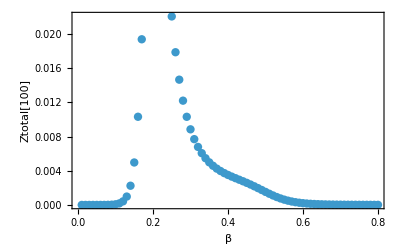

```mathematica
(*Bifurcation:Sweep beta and plot Ztotal[100]*)
bifurcationData=
Reap[
Do[
Module[
{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},
paramsLocal=params;
paramsLocal["beta"]=b;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];

If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];

If[NumericQ[Zfinal],Sow[{b,Zfinal}]]]],
{b,0.01,0.8,0.01}]][[2,1]];

(*Plot*)
ListPlot[bifurcationData,Frame->True,FrameLabel->{"β","Ztotal[100]"},PlotStyle->PointSize[0.015]]
```

### 1D Bifurcation sweep: Dimensionless bifurcation of R0 and sample at fixed τ

InterpolatingFunction::dmval: Input value {1000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

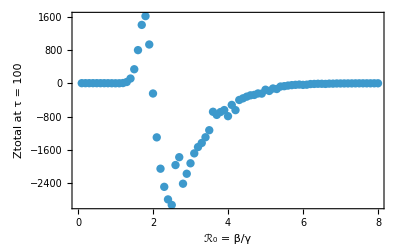

```mathematica
τEnd=100;                 (*dimensionless time:τ=γ t*)
r0Min=0.1;
r0Max=8;
r0Step=0.1;

bifurcationDataR0=
Reap[
Do[
Module[
{p=params,sol,Z1f,Z2f,Z3f,tSample,Zfinal},
p["beta"]=r0*p["gamma"];

(*β=R0·γ*)
sol=Quiet@Check[simulateZombieSystem[p],$Failed];
If[
ListQ[sol],
Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
tSample=τEnd/p["gamma"];

(*t=τ/γ*)
Zfinal=Z1f[tSample]+Z2f[tSample]+Z3f[tSample];
If[
NumericQ[Zfinal],
Sow[{r0,Zfinal}]]]],
{r0,r0Min,r0Max,r0Step}
]
][[2,1]];

ListPlot[bifurcationDataR0,Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(ℛ\), \(0\)]\) = β/γ",Row[{"Ztotal at τ = ",τEnd}]},PlotStyle->PointSize[0.015],FrameTicks->All]
```

### 1D Bifurcation Sweep: Recovery Rate

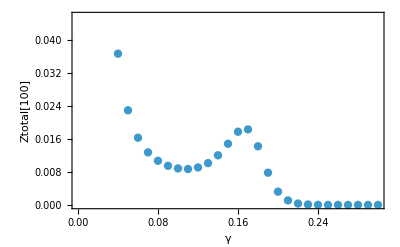

```mathematica
(*Bifurcation:Sweep gamma and plot Ztotal[100]*)
bifurcationDataGamma=Reap[
Do[
Module[
{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},
paramsLocal=params;
paramsLocal["gamma"]=g;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];

If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[
NumericQ[Zfinal],
Sow[{g,Zfinal}]
]
]
],

{g,0.01, 0.3,0.01}
]
][[2,1]];

(*Plot*)
ListPlot[bifurcationDataGamma,Frame->True,FrameLabel->{"γ","Ztotal[100]"},PlotStyle->PointSize[0.015]]
```

### 1D Interaction Rate Sweep

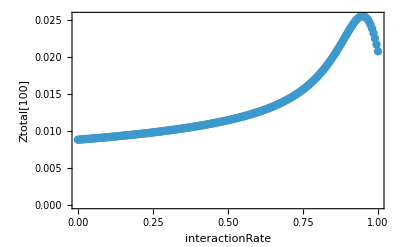

```mathematica
(*Bifurcation:Sweep interactionRate and plot Ztotal[100]*)
bifurcationDataInteraction=Reap[
Do[
Module[
{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},
paramsLocal=params;
paramsLocal["interactionRate"]=r;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];

If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];

If[NumericQ[Zfinal],Sow[{r,Zfinal}
]
]
]
],
{r,0.0,1,0.005}
]
][[2,1]];

(*Plot*)
ListPlot[bifurcationDataInteraction,Frame->True,FrameLabel->{"interactionRate","Ztotal[100]"},PlotStyle->PointSize[0.015]]
```

### 1D Prey growth rate Sweep

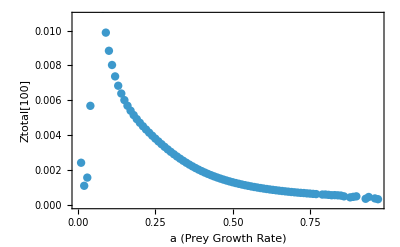

```mathematica
(*Bifurcation:Sweep prey growth rate a and plot Ztotal[100]*)bifurcationDataA=Reap[Do[Module[{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},paramsLocal=params;
paramsLocal["a"]=a;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];

If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[Zfinal],Sow[{a,Zfinal}
]
]
]
],
{a,0.01,1,0.01}
]
][[2,1]];

(*Plot*)
ListPlot[bifurcationDataA,Frame->True,FrameLabel->{"a (Prey Growth Rate)","Ztotal[100]"},PlotStyle->PointSize[0.015]]
```

```mathematica
(* ===3D map:sweep β,γ,a;plot Ztotal[100],color by a===*)betaRange=Range[0.10,0.50,0.05];
gammaRange=Range[0.05,0.30,0.025];
aRange=Range[0.05,0.30,0.05];

data3D=Reap[
Do[
Module[
{p=params,sol,Z1f,Z2f,Z3f,zFinal},
p["beta"]=b;
p["gamma"]=g;
p["a"]=a;
sol=Quiet@Check[simulateZombieSystem[p],$Failed];

If[ListQ[sol],
Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
zFinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[zFinal],Sow[{b,g,a,zFinal}]]]],{b,betaRange},{g,gammaRange},{a,aRange}
]
][[2,1]];

If[data3D==={},Print["No data collected (all simulations failed)."],

(*Build coloured 3D scatter:x=β,y=γ,z=Ztotal[100],colour=a*)

With[
{amin=Min[aRange],
amax=Max[aRange],
cmap=ColorData["BlueGreenYellow"]
},

Legended[
Graphics3D[
Table[With
[{b=row[[1]],g=row[[2]],a=row[[3]],z=row[[4]],col=cmap[Rescale[row[[3]],{amin,amax}]]},
{col,PointSize[0.013],Point[{b,g,z}]}],
{row,data3D}],
Axes->True,
AxesLabel->(Style[#,13]&/@{"β","γ","Ztotal[100]"}),
BoxRatios->{1,1,0.7},
PlotRange->All,
Lighting->"Neutral"],
BarLegend[{cmap,{amin,amax}},
LegendLabel->Style["a (prey growth rate)",12],
LabelStyle->10]
]
]
]
```

-Graphics3D-

### 1D Predator efficiency sweep

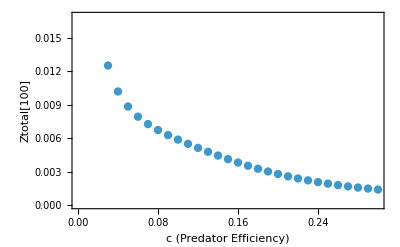

```mathematica
(*Bifurcation:Sweep predator efficiency c and plot Ztotal[100]*)bifurcationDataC=Reap[Do[Module[{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},paramsLocal=params;
paramsLocal["c"]=c;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];
If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[Zfinal],Sow[{c,Zfinal}
]
]
]
],
{c,0.01,0.3,0.01}
]
][[2,1]];

(*Plot*)
ListPlot[bifurcationDataC,Frame->True,FrameLabel->{"c (Predator Efficiency)","Ztotal[100]"},PlotStyle->PointSize[0.015]]
```

```mathematica
sol = simulateZombieSystem["beta" -> 0.1]
```

simulateZombieSystem[beta→0.1]

## 2D Bifurcation sweeps

### Beta VS Interaction Rate

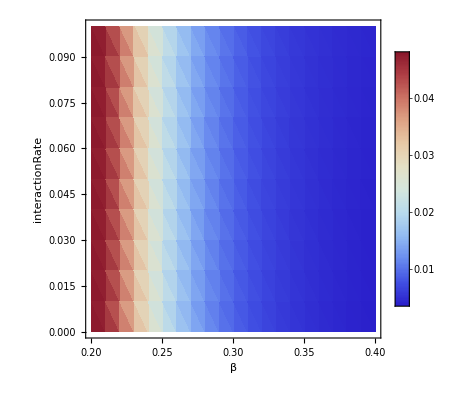

```mathematica
(*Bifurcation:Sweep beta and interactionRate,plot Ztotal[100]*)
bifurcationData=Reap[Do[Do[Module[{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},paramsLocal=params;
paramsLocal["beta"]=b;
paramsLocal["interactionRate"]=iRate;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];
If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[Zfinal],Sow[{b,iRate,Zfinal}
]
]
]
],
{iRate,0,0.1,0.01}
],
{b,0.2,0.4,0.01}]][[2,1]];

(*ListDensityPlot[bifurcationData,FrameLabel->{"β","interactionRate","Ztotal[100]"},ColorFunction->ColorData["BlueGreenYellow"],PlotLegends->Automatic]*)
ListDensityPlot[
bifurcationData,
InterpolationOrder->1,
FrameLabel->{"β","interactionRate","Ztotal[100]"},
ColorFunction->"ThermometerColors",
PlotLegends->Automatic,
Frame->True,
PlotRange->All,
Mesh->None
]
```

### Beta VS gamma

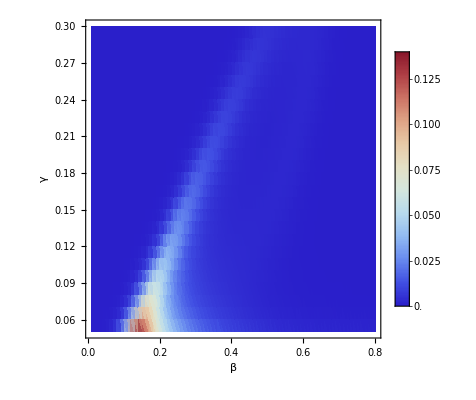

```mathematica
(*Bifurcation:Sweep beta and gamma,plot Ztotal[100]*)bifurcationDataBetaGamma=Reap[Do[Do[Module[{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},paramsLocal=params;
paramsLocal["beta"]=b;
paramsLocal["gamma"]=g;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];
If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[Zfinal],Sow[{b,g,Zfinal}]]]],{g,0.05,0.3,0.01}],{b,0.01,0.8,0.01}]][[2,1]];

(*Density plot of beta vs gamma sweep*)
ListDensityPlot[
bifurcationDataBetaGamma,
InterpolationOrder->1,
FrameLabel->{"β","γ","Ztotal[100]"},
ColorFunction->"ThermometerColors",
PlotLegends->Automatic,
Frame->True,
PlotRange->All,
Mesh->None
]
```

### a vs c

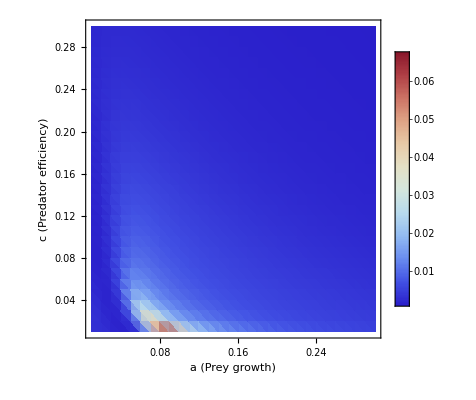

```mathematica
(* Bifurcation: Sweep a (prey growth) and c (predator efficiency), plot Ztotal[100] *)
bifurcationDataAC = 
  Reap[
    Do[
      Do[
        Module[{paramsLocal, sol, Z1f, Z2f, Z3f, Zfinal}, 
         paramsLocal = params;
         paramsLocal["a"] = a;
         paramsLocal["c"] = c;
         sol = Quiet@Check[simulateZombieSystem[paramsLocal], $Failed];
         If[ListQ[sol], 
          Z1f = Z1 /. sol;
          Z2f = Z2 /. sol;
          Z3f = Z3 /. sol;
          Zfinal = Z1f[100] + Z2f[100] + Z3f[100];
          If[NumericQ[Zfinal], Sow[{a, c, Zfinal}]]
         ]
        ],
        {c, 0.01, 0.3, 0.01}
      ],
      {a, 0.01, 0.3, 0.01}
    ]
  ][[2, 1]];

(* Plot the bifurcation map *)
ListDensityPlot[
  bifurcationDataAC,
  InterpolationOrder -> 1,
  FrameLabel -> {"a (Prey growth)", "c (Predator efficiency)", "Ztotal[100]"},
  ColorFunction -> "ThermometerColors",
  PlotLegends -> Automatic,
  Frame -> True,
  PlotRange -> All,
  Mesh -> None
]
```

### beta VS ABeta

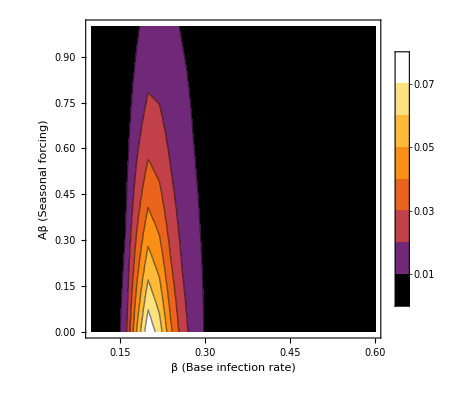

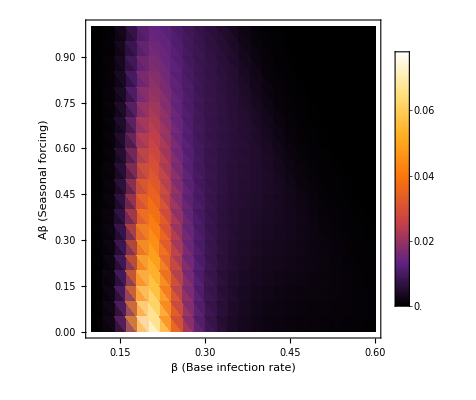

```mathematica
(*Bifurcation:Sweep β and Aβ,plot Ztotal[100]*)bifurcationDataBetaAβ=Reap[Do[Do[Module[{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},paramsLocal=params;
paramsLocal["beta"]=β;
paramsLocal["Aβ"]=Aβ;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];
If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[Zfinal],Sow[{β,Aβ,Zfinal}]]]],{Aβ,0,1,0.05}],{β,0.1,0.6,0.02}]][[2,1]];

(*Plot result*)
ListContourPlot[
bifurcationDataBetaAβ,
InterpolationOrder->1,
FrameLabel->{"β (Base infection rate)","Aβ (Seasonal forcing)","Ztotal[100]"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
Frame->True,
PlotRange->All,
Mesh->None]

ListDensityPlot[
bifurcationDataBetaAβ,
InterpolationOrder->1,
FrameLabel->{"β (Base infection rate)","Aβ (Seasonal forcing)","Ztotal[100]"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
Frame->True,
PlotRange->All,
Mesh->None
]
```

### beta VS Aa seasonsal amplitude of prey growth rate

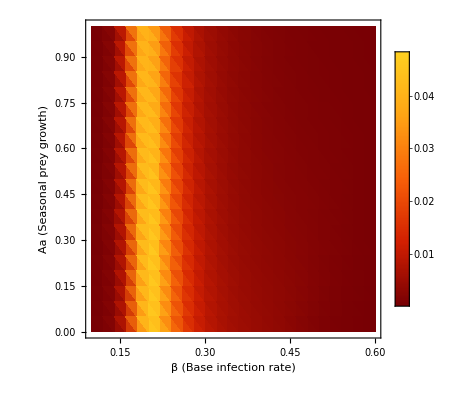

```mathematica
(*Bifurcation:Sweep β and Aa,plot Ztotal[100]*)bifurcationDataBetaAa=Reap[Do[Do[Module[{paramsLocal,sol,Z1f,Z2f,Z3f,Zfinal},paramsLocal=params;
paramsLocal["beta"]=β;
paramsLocal["Aa"]=Aa;
sol=Quiet@Check[simulateZombieSystem[paramsLocal],$Failed];
If[ListQ[sol],Z1f=Z1/. sol;
Z2f=Z2/. sol;
Z3f=Z3/. sol;
Zfinal=Z1f[100]+Z2f[100]+Z3f[100];
If[NumericQ[Zfinal],Sow[{β,Aa,Zfinal}]]]],{Aa,0,1,0.05}],{β,0.1,0.6,0.02}]][[2,1]];

(*Plot result*)
ListDensityPlot[
bifurcationDataBetaAa,
InterpolationOrder->1,
FrameLabel->{"β (Base infection rate)","Aa (Seasonal prey growth)","Ztotal[100]"},
ColorFunction->"SolarColors",
PlotLegends->Automatic,
Frame->True,
PlotRange->All,
Mesh->None
]
```

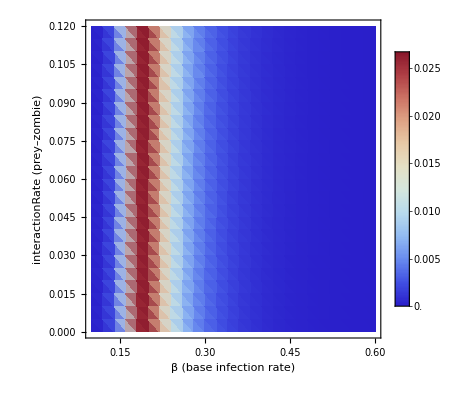

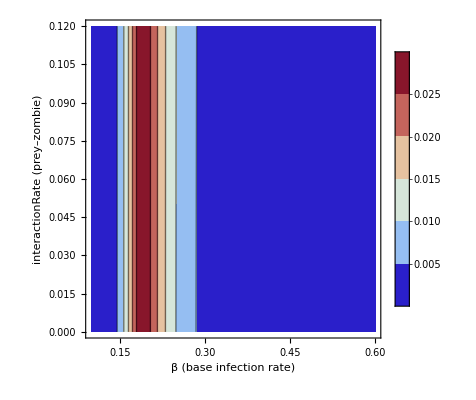

```mathematica
(*Bifurcation:Sweep β and interactionRate,plot Ztotal[100]*)
bifurcationDataBetaIR=Reap[
Do[
Do[
Module[
{p=params,sol,Z1f,Z2f,Z3f,Zfinal},p["beta"]=b;
p["interactionRate"]=ir;
sol=Quiet@Check[simulateZombieSystem[p],$Failed];

If[
ListQ[sol],Z1f=Z1/. sol;Z2f=Z2/. sol;Z3f=Z3/. sol;

Zfinal=Z1f[100]+Z2f[100]+Z3f[100];

If[NumericQ[Zfinal],Sow[{b,ir,Zfinal}]]]],{ir,0.0,0.12,0.005}   (*distraction strength sweep*)],{b,0.10,0.60,0.02}      (*infection rate sweep*)]][[2,1]];

(*Plot result*)
ListDensityPlot[
bifurcationDataBetaIR,
InterpolationOrder->1,
Frame->True,
FrameLabel->{"β (base infection rate)","interactionRate (prey–zombie)","Ztotal[100]"},
ColorFunction->"ThermometerColors",
PlotLegends->Automatic,
PlotRange->All,
Mesh->None
]

ListContourPlot[
bifurcationDataBetaIR,
InterpolationOrder->1,
Frame->True,
FrameLabel->{"β (base infection rate)","interactionRate (prey–zombie)","Ztotal[100]"},
ColorFunction->"ThermometerColors",
PlotLegends->Automatic,
PlotRange->All,
Mesh->None
]
```